```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

### import

```mathematica
{directR,directT,directA}=Import["data_tradeoffs//directRecognitionPoints_rta.mx"];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

```mathematica
{guardR,guardT,guardA,guardComplex}=Import["data_tradeoffs//guardModelPoints_rta_complex.mx"];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

### get transition points and target levels

```mathematica
(*get point data*)
```

```mathematica
(*find the transition point: first activating E0*)
getTransitionPt[inputPoints_]:=Module[{thisTally,annihilationPts,multiSS,i,thisPoint},

thisTally=inputPoints[[;;,1]]//Tally;
annihilationPts={};

multiSS=False;
For[i=1,i<=Length[thisTally],i++,

thisPoint=thisTally[[i]];
If[thisPoint[[2]]>1,multiSS=True];
If[multiSS==True&&thisPoint[[2]]==1,AppendTo[annihilationPts,thisPoint[[1]]];multiSS=False];

];
multiSS=False;
annihilationPts[[1]]
];
```

```mathematica
getTransitionTargetConcentration[targetPoints_]:=Module[{thisTransitionPoint,transitionIndex,postTransition,postTransitionFP,preTransition,preTransitionFP,ratio},

thisTransitionPoint=getTransitionPt[targetPoints];
Print[thisTransitionPoint];

transitionIndex=Position[targetPoints,thisTransitionPoint][[1,1]];
postTransition=targetPoints[[transitionIndex]];
postTransitionFP=postTransition[[2]];


postTransitionFP
]
```

```mathematica
guardTransitionPoint=getTransitionPt[guardT]
directTransitionPoint=getTransitionPt[directT]
(*decoyTransitionPoint=getTransitionPt[decoyT]*)
```

3.8

6.3

```mathematica
(*guardRatio=getTargetRatio[guardT,3];*)
guardTargetLevel=getTransitionTargetConcentration[guardT];
```

3.8

```mathematica
(*directRatio=getTargetRatio[directT,1];*)
directTargetLevel=getTransitionPt[directT];
```

```mathematica
(*decoyRatio=getTargetRatio[decoyT,3];*)
```

### decoy curve

```mathematica
decoygDList={10,12,15,20};
```

```mathematica
decoyPoints={};
```

```mathematica
For[i=1,i<=Length[decoygDList],i++,

thisGD=decoygDList[[i]];
{thisR,thisT,thisA,thisD}=Import["data_tradeoffs//decoyPoints_gD_"<>ToString[thisGD]<>"_rtad.mx"];

AppendTo[decoyPoints,{getTransitionPt[thisT],getTransitionTargetConcentration[thisT]}];

]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

Part::partw: Part 4 of {}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

7.1

5.6

4.6

3.9

### plot summary points

```mathematica
(*guardPoint={guardTransitionPoint,guardRatio};
directPoint={directTransitionPoint,directRatio};*)
```

```mathematica
guardPoint={guardTransitionPoint,guardTargetLevel};
directPoint={directTransitionPoint,directTargetLevel};
```

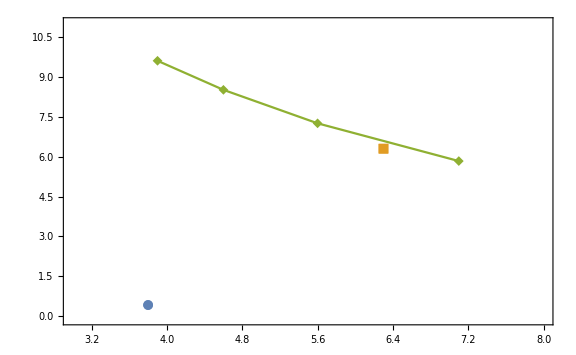

```mathematica
plot=ListPlot[{{guardPoint},{directPoint},decoyPoints},(*PlotLegends->{"Guard", "Direct","Decoy"},*)LabelStyle->Directive[Black, 25],Frame->{True,True,False,False},Joined->{False,False,True},(*FrameLabel->{"Activating effector load E_1^*","Target concentration after activation"},*)PlotMarkers->{Automatic,Medium},ImageSize->Large,PlotRange->{{3,8},{-.1,11}}]
```

```mathematica
label1=Graphics[Text["g_D=10",{7,6}]];
```

```mathematica
labelList=Table[Graphics[Text[Style["g_D="<>ToString[decoygDList[[i]]],25],{decoyPoints[[i,1]],decoyPoints[[i,2]]+0.9}]],{i,Length[decoygDList]}];
```

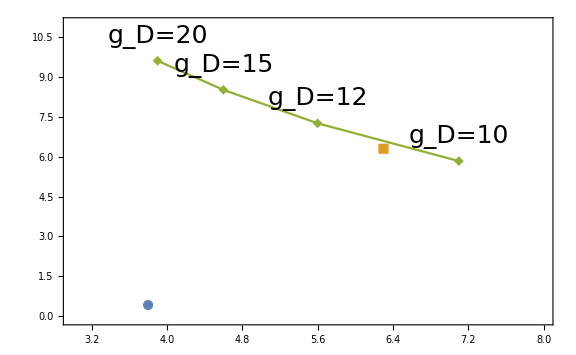

```mathematica
labeledPlot=Show[plot,labelList]
```

```mathematica
(*Export["tradeoffPlot.png",%,ImageResolution->200]*)
```

tradeoffPlot.png

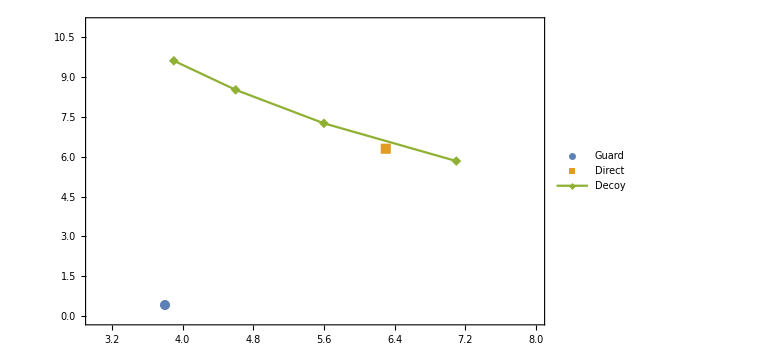

```mathematica
ListPlot[{{guardPoint},{directPoint},decoyPoints},PlotLegends->{"Guard", "Direct","Decoy"},LabelStyle->Directive[Black, 25],Frame->{True,True,False,False},Joined->{False,False,True},(*FrameLabel->{"Activating effector load E_1^*","Target concentration after activation"},*)PlotMarkers->{Automatic,Medium},ImageSize->Large,PlotRange->{{3,8},{-.1,11}}]
```

```mathematica
(*Export["tradeoffPlot_legends.png",%,ImageResolution->200]*)
```

tradeoffPlot_legends.png